```mathematica
tStart = AbsoluteTime[];
```

```mathematica
Clear[Lx, Ly, A, l, mL,
 SX2DSingDis,SY2DSingDis,
 CX2DSingDis,CY2DSingDis,
SX2DPSingDis,CX2DPSingDis,
 Cons]
```

```mathematica
Lx = 60;
Ly = 60;
l = Ly/2;
mL = Lx/2;
A = Lx*Ly + Ly-l
NOrbitals = 2*A;
```

3630

```mathematica
(**------------------------------------**)
```

```mathematica
SX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SX2DSingDis[[a + b Lx, a + 1 + b Lx]]=I/2, SX2DSingDis[[a + 1 + b Lx, a + b Lx]] = -I/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{SX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=I/2, SX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=-I/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
SX2DPSingDis=Table[0,{a,1,A},{b,1,A}];
Do[{SX2DPSingDis[[Lx + b Lx, 1 + b Lx]]=I/2, SX2DPSingDis[[1 + b Lx, Lx + b Lx]] = -I/2},{b,0, l-1}]
Do[{SX2DPSingDis[[Lx+1+b (Lx+1)+l *Lx,1+b (Lx+1)+l *Lx]]=I/2, SX2DPSingDis[[1+b (Lx+1)+l *Lx,Lx+1+b (Lx+1)+l *Lx]]=-I/2},{b,0,Ly-1-l}]
```

```mathematica
HermitianMatrixQ[SX2DPSingDis]
```

True

```mathematica
(**------------------------------------**)
```

```mathematica
CX2DSingDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CX2DSingDis[[a + b Lx, a + 1 + b Lx]]=1/2, CX2DSingDis[[a + 1 + b Lx, a + b Lx]] = 1/2},{a,1, Lx -1}],{b,0, l-1}]
Do[Do[{CX2DSingDis[[a+b (Lx+1)+l *Lx,a+1+b (Lx+1)+l *Lx]]=1/2, CX2DSingDis[[a+b (Lx+1)+l *Lx+1,a+b (Lx+1)+l *Lx]]=1/2},{a,1,Lx}],{b,0,Ly-1-l}]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CX2DPSingDis=Table[0,{a,1,A},{b,1,A}];
Do[{CX2DPSingDis[[Lx + b Lx, 1 + b Lx]]=1/2, CX2DPSingDis[[1 + b Lx, Lx + b Lx]] = 1/2},{b,0, l-1}]
Do[{CX2DPSingDis[[Lx+1+b (Lx+1)+l *Lx,1+b (Lx+1)+l *Lx]]=1/2, CX2DPSingDis[[1+b (Lx+1)+l *Lx,Lx+1+b (Lx+1)+l *Lx]]=1/2},{b,0,Ly-1-l}]
```

```mathematica
HermitianMatrixQ[CX2DPSingDis]
```

True

```mathematica
(**------------------------------------**)
```

```mathematica
SY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{SY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=I/2, SY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = -I/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{SY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=I/2, SY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = -I/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{SY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=I/2, SY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = -I/2},{a,1,mL }]
Do[{SY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=I/2, SY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = -I/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
CY2DSingDis=Table[0,{a,1,A},{b,1,A}];
(**lower block**)
Do[Do[{CY2DSingDis[[a + b Lx, a + (1+ b) Lx]]=1/2, CY2DSingDis[[a +(1 + b) Lx, a + b Lx]] = 1/2},{a,1, Lx }],{b,0, l-2}]
(**upper block**)
Do[Do[{CY2DSingDis[[a + b (Lx+1)+l*Lx, a + (b+1) (Lx+1)+l*Lx]]=1/2, CY2DSingDis[[a + (b+1) (Lx+1)+l*Lx, a + b (Lx+1)+l*Lx]] = 1/2},{a,1, Lx+1 }],{b,0, Ly-l-2}]
(**connectors**)
Do[{CY2DSingDis[[a + (l-1)*Lx, a +l*Lx]]=1/2, CY2DSingDis[[a +l*Lx, a +(l-1)*Lx]] = 1/2},{a,1,mL }]
Do[{CY2DSingDis[[a + mL+(l-1)*Lx, a +mL+1+l*Lx]]=1/2, CY2DSingDis[[a +mL+1+l*Lx, a + mL+(l-1)*Lx]] = 1/2},{a,1,Lx-mL }]
```

```mathematica
(**------------------------------------**)
```

```mathematica
Cons=Table[0,{a,1,A},{b,1,A}];
Do[Cons[[a,a]]=1,{a,1,A}]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHIDisloc]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHIDisloc[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2DSingDis + α SX2DPSingDis,σ1]+KroneckerProduct[SY2DSingDis, σ2])+KroneckerProduct[m*Cons-t0*(CX2DSingDis+ α CX2DPSingDis+CY2DSingDis),σ3]
```

```mathematica
(**---------------------------------------------------------**)
```

```mathematica
Clear[Xaxis, Yaxis1, Yaxis2, Yaxis3, P3, P4, P2B]
```

```mathematica
Xaxis=Table[{{1,j},{Lx+1,j}},{j,1,Ly,1}];
```

```mathematica
Dimensions[Xaxis]
```

{60,2,2}

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,Ly}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2,29},None}},BaseStyle-> 18];
```

```mathematica
Yaxis1=Table[{{j,1},{j,Ly}},{j,1,mL,1}];
```

```mathematica
Yaxis2={{mL+1,l+1},{mL+1,Ly}};
```

```mathematica
Yaxis3=Table[{{j,1},{j,Ly}},{j,mL+2,Lx+1,1}];
```

```mathematica
Dimensions[Yaxis3]
```

{30,2,2}

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
ListPlot[Yaxis2,Joined-> True,PlotStyle-> Lighter[Gray]],
ListPlot[Table[Yaxis3[[j]],{j,1,Lx-mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}}]
];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},
Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,Round[Ly/4]+1,Round[3 Ly/4],Ly},None},{{1,Round[Lx/2]+1,Lx+1},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P5=Show[P2B,P3,P4];
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

7200

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
LineUp[x_]:=(2/3)*(x-1)+12
LineDn[x_]:=(2/3)*(x-2)+10
```

```mathematica
N[LineUp[6]]
```

15.3333

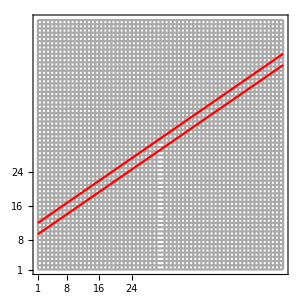

```mathematica
Show[P5,
Plot[LineUp[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
Plot[LineDn[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
(**---This function generates site number for a given coordinates and set of parameter---**)
```

```mathematica
(**---Generates 0 for non existing points, e.g. the two lines below and above dislocation centers---**)
```

```mathematica
GenerateSiteNumber[x_,y_,Lx_,Ly_,l_,mL_]:=Piecewise[{{x+(y-1)Lx, 1≤ x ≤ mL &&1≤ y≤ l },{x+(y-1)Lx-1, Lx+1≥ x > mL+1 &&1≤ y≤ l},{x+(y-1)(Lx+1)-l,l<y≤Ly&&Lx+1≥ x ≥ 1 }},0]
```

```mathematica
(** Dislocation center site number **)
```

```mathematica
GenerateSiteNumber[15,15,Lx,Ly,l,mL]
```

855

```mathematica
28*14+15
```

407

```mathematica
Clear[FibonListNew]
FibonListNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
(**--x runs from 1 to Lx + 1--**)
```

```mathematica
Do[Do[FibonListNew=Append[FibonListNew,GenerateSiteNumber[x,y,Lx,Ly,l,mL]],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx+1}]
```

```mathematica
FibonList=Sort[FibonListNew]
```

{0,541,601,602,603,662,663,664,723,724,725,726,785,786,787,846,847,848,849,908,909,910,969,970,971,972,1031,1032,1033,1092,1093,1094,1095,1154,1155,1156,1215,1216,1217,1218,1277,1278,1279,1338,1339,1340,1341,1400,1401,1402,1461,1462,1463,1464,1523,1524,1525,1584,1585,1586,1587,1646,1647,1648,1707,1708,1709,1710,1769,1770,1830,1831,1832,1833,1893,1894,1895,1955,1956,1957,1958,2018,2019,2020,2080,2081,2082,2083,2143,2144,2145,2205,2206,2207,2208,2268,2269,2270,2330,2331,2332,2333,2393,2394,2395,2455,2456,2457,2458,2518,2519,2520,2580,2581,2582,2583,2643,2644,2645,2705,2706,2707,2708,2768,2769,2770,2830,2831,2832,2833,2893,2894,2895,2955,2956,2957,2958,3018,3019,3020,3080,3081}

```mathematica
(**--Delete the zeros, which are generated for the non-existing lines of atoms--**)
```

```mathematica
FibonList=DeleteCases[FibonList,0]
```

{541,601,602,603,662,663,664,723,724,725,726,785,786,787,846,847,848,849,908,909,910,969,970,971,972,1031,1032,1033,1092,1093,1094,1095,1154,1155,1156,1215,1216,1217,1218,1277,1278,1279,1338,1339,1340,1341,1400,1401,1402,1461,1462,1463,1464,1523,1524,1525,1584,1585,1586,1587,1646,1647,1648,1707,1708,1709,1710,1769,1770,1830,1831,1832,1833,1893,1894,1895,1955,1956,1957,1958,2018,2019,2020,2080,2081,2082,2083,2143,2144,2145,2205,2206,2207,2208,2268,2269,2270,2330,2331,2332,2333,2393,2394,2395,2455,2456,2457,2458,2518,2519,2520,2580,2581,2582,2583,2643,2644,2645,2705,2706,2707,2708,2768,2769,2770,2830,2831,2832,2833,2893,2894,2895,2955,2956,2957,2958,3018,3019,3020,3080,3081}

```mathematica
(** Dislocation center is in 108th position --- orbitals are 215 and 216 **)
```

```mathematica
Dimensions[FibonList]
```

{141}

```mathematica
Clear[Fibonup, Fibondown, TotalFibon]
```

```mathematica
Fibonup = 2 * FibonList -1;
```

```mathematica
Fibondown = 2* FibonList;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon=Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

282

```mathematica
NOrbitalsQuasi/2
```

141

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

6918

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{7260}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
Dimensions[a]
```

{6978}

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHIDisloc[1.,1.,-0.005,1];
```

```mathematica
Clear[ SX2DSingDis,SY2DSingDis,
 CX2DSingDis,CY2DSingDis,
SX2DPSingDis,CX2DPSingDis,
 Cons]
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
Clear[Hfbfb]
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
Clear[H2d2d]
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
Clear[H2dfb]
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
Clear[Hfb2d]
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial]
```

```mathematica
(**+ 0.00001 IdentityMatrix[NOrbitalsOutside] **)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D- 0.000001 IdentityMatrix[NOrbitalsOutside]].H2DFB);
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{Re[ValueFibon],VecFibon}],First];
```

```mathematica
ValFibon=Re[Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]]//Chop;
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

0.255197

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{i,0,
Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2
},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]/2},{i,1,3*NOrbitalsQuasi/2,3}];
```

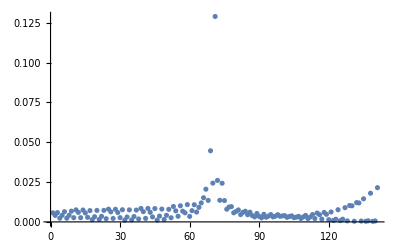

```mathematica
ListPlot[Table[{TDFibon[[i]],TDFibon[[i+2]]/2},{i,1,3*NOrbitalsQuasi/2,3}],PlotRange->All]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
(** Blue **)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.2*v/vmax,1,1.0-0.3 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.2 v)/vmax,1,1.-(0.3 v)/vmax,v/vmax]]

```mathematica
colorfuncRedBlue=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
(** Black and White **)
```

```mathematica
colorfuncBW=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.5 v)/vmax,0,1.-(1. v)/vmax,v/vmax]]

```mathematica
rngOld={0,Max[#]}&@TabFibonacci[[All,3]]
```

{0,0.128993}

```mathematica
rng = {0,0.17}
```

{0,0.17}

```mathematica
rng[[2]]
```

0.17

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.12"},{rng[[2]]-10^-3,"0.24"}}]
```

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX+1},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[largestX-1,{largestX-1,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
];
```

ListPlot::lpn: Fibon1D is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Fibon1D,PlotStyle→{color,PointSize[0.015]}],Epilog→{Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[-1+largestX,{-1+largestX,-2.5}],Inset[BarLegend[{«1»&,{«2»}},LabelStyle→{«2»},Ticks→{«3»}],{10.5,5.}],Inset[m=1.5,{21.5,7}],Inset[(a),{1.25,7}]}].

```mathematica
SiteIndex=Table[{i,0},{i,1,NOrbitalsQuasi/2}];
```

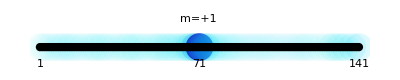

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
BaseStyle-> 18,
PlotRange-> {{-0.5,NOrbitalsQuasi/2+2},{-4.5,7}}],
ListPlot[SiteIndex,PlotStyle-> {Black,PointSize[0.015]}],
Epilog-> {Inset[1,{1,-3}],Inset[Ceiling[NOrbitalsQuasi/4],{Ceiling[NOrbitalsQuasi/4],-3}],Inset[NOrbitalsQuasi/2,{NOrbitalsQuasi/2,-3}],Inset["m=+1",{NOrbitalsQuasi/4,5}]
}
]
```

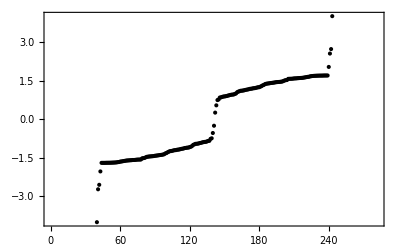

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
(** Need to export ValFibon and TabFibonacci **)
```

```mathematica
Export["LDOSParent60DislocationRational10to12mM0005PBC.dat",TabFibonacci]
```

LDOSParent60DislocationRational10to12mM0005PBC.dat

```mathematica
tStop = AbsoluteTime[];
```

```mathematica
timeTakenInSeconds = tStop - tStart
```

556.57966